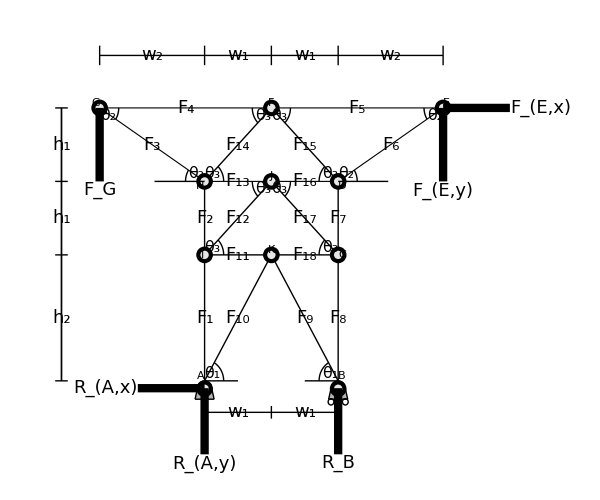

```mathematica
Module[{w1,w2,h1,h2,δh,δw,θ1,θ2,θ3,truss,measurements},
w1=7;w2=11;h1=7;h2=12;
δh=2*h1+h2+5;δw=-w1-w2-4;
θ1=ArcTan[h2/w1];θ2=ArcTan[h1/w2];θ3=ArcTan[h1/w1];

truss=Graphics[{Thick,
(*DRAWING TRUSS*)
{EdgeForm@Thick,FaceForm@None,Polygon[{{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{w1,h1+h2},{-w1,h1+h2}}]},
{Line[{{#*w1,h1+h2},{0,2*h1+h2}}],Line[{{#*w1,h2},{0,h1+h2}}],Line[{{#*w1,0},{0,h2}}]}&/@{-1,1},
Line[{{#,h1+h2},{#,0}}]&/@{-w1,w1},
Line[{{-w1,h2},{w1,h2}}],


{Thick,{GrayLevel@0.7,Disk[{#*w1,-0.75},0.75],Polygon[{{#*w1-0.75,-0.75/2},{#*w1+0.75,-0.75/2},{#*w1+1,-1.75},{#*w1-1,-1.75}}]},
Line[{{#*w1-0.75,-0.75},{#*w1-1,-1.75}}],
Line[{{#*w1+0.75,-0.75},{#*w1+1,-1.75}}],
Line[{{#*w1-1,-1.75},{#*w1+1,-1.75}}],
Line@Table[{i,√(0.75^2-(i-#*w1)^2)-0.75},{i,#*w1-0.75,#*w1+0.75,0.1}]}&/@{-1,1},

{EdgeForm@Thick,FaceForm@None,Circle[{w1+#,-2},0.3]}&/@{-0.75,0,0.75},

{PointSize@0.02,Point@#,GrayLevel@0.9,PointSize@0.01,Point@#}&/@{{-w1,-0.75},{w1,-0.75},{-w1,h2},{w1,h2},{-w1,h1+h2},{w1,h1+h2},{0,h2},{0,h1+h2},{0,2*h1+h2},{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2}},

(*JOINTS*)
Text[Framed[Style[Row@{" ",#1," "},16],RoundingRadius->20,FrameMargins->Tiny],#2,#3]&@@@{{"A",{-w1,0},{1.5,-0.5}},{"B",{w1,0},{-1.5,-0.5}},{"C",{w1,h2},{-1.5,0}},{"D",{w1,h1+h2},{-1.5,2}},{"E",{w1+w2,2*h1+h2},{-1,-1.5}},{"F",{0,2*h1+h2},{0,-1.5}},{"G",{-w1-w2,2*h1+h2},{1,-1.5}},{"H",{-w1,h1+h2},{1.5,2}},{" I ",{-w1,h2},{1.5,0}},{"J",{0,h1+h2},{0,-1.5}},{"K",{0,h2},{0,-1.5}}},

Text[Style[Subscript[Style["θ",Italic],#1],16],#2,#3]&@@@{
{1,{-w1,0},{-3.5,-1.2}},{1,{w1,0},{3.5,-1.2}},
{2,{-w1,h1+h2},{3.5,-1}},{2,{w1,h1+h2},{-3.5,-1}},
{2,{-w1-w2,2*h1+h2},{-3.5,1}},{2,{w1+w2,2*h1+h2},{3.5,1}},
{3,{0,2*h1+h2},{3.5,1.2}},{3,{0,2*h1+h2},{-3.5,1.2}},
{3,{-w1,h1+h2},{-3.5,-2}},{3,{w1,h1+h2},{3.5,-2}},
{3,{0,h1+h2},{3.5,2}},{3,{0,h1+h2},{-3.5,2}},
{3,{-w1,h2},{-3.5,-2}},{3,{w1,h2},{3.5,-2}}},
{Thin,Line[{{#*w1,0},{#*0.5*w1,0}}],Line[{{#*w1,h1+h2},{#*1.75*w1,h1+h2}}]}&/@{-1,1},
{Thin,
Circle[{-w1-w2,2*h1+h2},2,{-θ2,0}],Circle[{w1+w2,2*h1+h2},2,{π,π+θ2}],
Circle[{0,2*h1+h2},2,{π,π+θ3}],Circle[{0,2*h1+h2},2,{-θ3,0}],
Circle[{-w1,h1+h2},2,{0,θ3}],Circle[{w1,h1+h2},2,{π/2+θ3,π}],
Circle[{-w1,h1+h2},2,{π-θ2,π}],Circle[{w1,h1+h2},2,{0,θ2}],
Circle[{0,h1+h2},2,{π,π+θ3}],Circle[{0,h1+h2},2,{-θ3,0}],
Circle[{-w1,h2},2,{0,θ3}],Circle[{w1,h2},2,{π/2+θ3,π}],
Circle[{-w1,0},2,{0,θ1}],Circle[{w1,0},2,{π-θ1,π}]}
},ImageSize->{600,500}];

measurements=Graphics[{
(*MEASUREMENTS*)
{Arrowheads@0,(*{-0.03,0.03},*)
Arrow[{{0,δh},{#*w1,δh}}],
Arrow[{{#*(w1+w2),δh},{#*w1,δh}}],
Arrow[{{#*w1,-3},{0,-3}}],
Arrow[{{δw,0},{δw,h2}}],Arrow[{{δw,h2},{δw,h1+h2}}],Arrow[{{δw,h1+h2},{δw,2*h1+h2}}]
}&/@{-1,1},
Line[{{#,0.97*δh},{#,1.03*δh}}]&/@{-w1-w2,-w1,0,w1,w1+w2},
Line[{{#,-0.8*3},{#,-1.2*3}}]&/@{-w1,0,w1},
Line[{{0.97*δw,#},{1.03*δw,#}}]&/@{0,h2,h1+h2,2*h1+h2},

{Text[Style[Subscript[Style["w",Italic],1],18,Background->White],{#*w1/2,δh}],
Text[Style[Subscript[Style["w",Italic],2],18,Background->White],{#*(w1+w2/2),δh}],
Text[Style[Subscript[Style["w",Italic],1],18,Background->White],{#*w1/2,-3}]}&/@{-1,1},
Text[Style[Subscript[Style["h",Italic],2],18,Background->White],{δw,h2/2}],
Text[Style[Subscript[Style["h",Italic],1],18,Background->White],{δw,h2+#*h1}]&/@{0.5,1.5},

{Thickness@0.01,Arrowheads@0.05,Arrow[{{#*(w1+w2),2*h1+h2},{#*(w1+w2),h1+h2}}]&/@{-1,1},Arrow[{{w1+w2,2*h1+h2},{w1+w2+h1,2*h1+h2}}],
Arrow[{{#*w1,-h1},{#*w1,-0.1*h1}}]&/@{-1,1},
Arrow[{{-w1,-0.1*h1},{-2*w1,-0.1*h1}}]},
Text[Style[Subscript[Style["F",Italic],"G"],18],{-w1-w2,h1+h2},{0,1.5}],
Text[Style[Subscript[Style["F",Italic],Row@{"E,",Style[#1,Italic]}],18],#2,#3]&@@@{{"x",{w1+w2+h1,2*h1+h2},{-1.5,0}},{"y",{w1+w2,h1+h2},{0,1.5}}},
Text[Style[Subscript[Style["R",Italic],Row@{"A,",Style[#1,Italic]}],18],#2,#3]&@@@{{"x",{-2*w1,-0.1*h1},{1,0}},{"y",{-w1,-h1},{0,1}}},
Text[Style[Subscript[Style["R",Italic],"B"],18],{w1,-h1},{0,1}],

(*Text[Framed[Style[Subscript[Style["F",Italic],#1],18],Background->White,FrameStyle->None,FrameMargins->None],#2]*)
Text[Style[Subscript[Style["F",Italic],#1],18,Background->White],#2]&@@@{{1,{-w1,h2/2}},{2,{-w1,h2+h1/2}},{3,{-w1-w2/2,1.5*h1+h2}},{4,{-(w1+w2)/2,2*h1+h2}},{5,{(w1+w2)/2,2*h1+h2}},{6,{w1+w2/2,1.5*h1+h2}},{7,{w1,h1/2+h2}},{8,{w1,h2/2}},{9,{w1/2,h2/2}},{10,{-w1/2,h2/2}},{11,{-w1/2,h2}},{12,{-w1/2,h1/2+h2}},{13,{-w1/2,h1+h2}},{14,{-w1/2,1.5*h1+h2}},{15,{w1/2,1.5*h1+h2}},{16,{w1/2,h1+h2}},{17,{w1/2,h1/2+h2}},{18,{w1/2,h2}}}
}];

Show[truss,measurements,PlotRange->{{-22.7,28.7},All}]
]
```

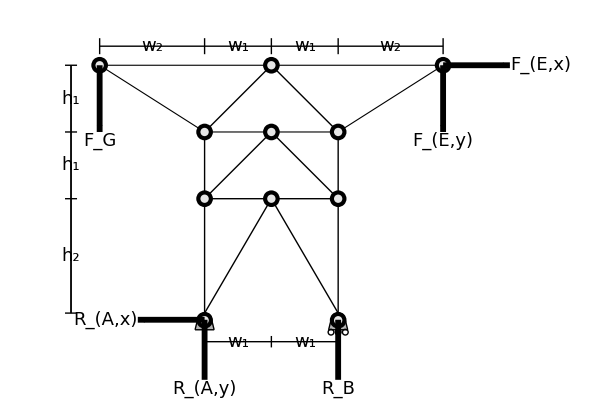

```mathematica
Module[{w1,w2,h1,h2,δh,δw,θ1,θ2,θ3,truss,measurements},
w1=7;w2=11;h1=7;h2=12;
δh=2*h1+h2+2;δw=-w1-w2-3;
θ1=ArcTan[h2/w1];θ2=ArcTan[h1/w2];θ3=ArcTan[h1/w1];

truss=Graphics[{Thick,
(*DRAWING TRUSS*)
{EdgeForm@Thick,FaceForm@None,Polygon[{{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2},{w1,h1+h2},{-w1,h1+h2}}]},
{Line[{{#*w1,h1+h2},{0,2*h1+h2}}],Line[{{#*w1,h2},{0,h1+h2}}],Line[{{#*w1,0},{0,h2}}]}&/@{-1,1},
Line[{{#,h1+h2},{#,0}}]&/@{-w1,w1},
Line[{{-w1,h2},{w1,h2}}],


{Thick,{GrayLevel@0.7,Disk[{#*w1,-0.75},0.75],Polygon[{{#*w1-0.75,-0.75/2},{#*w1+0.75,-0.75/2},{#*w1+1,-1.75},{#*w1-1,-1.75}}]},
Line[{{#*w1-0.75,-0.75},{#*w1-1,-1.75}}],
Line[{{#*w1+0.75,-0.75},{#*w1+1,-1.75}}],
Line[{{#*w1-1,-1.75},{#*w1+1,-1.75}}],
Line@Table[{i,√(0.75^2-(i-#*w1)^2)-0.75},{i,#*w1-0.75,#*w1+0.75,0.1}]}&/@{-1,1},

{EdgeForm@Thick,FaceForm@None,Circle[{w1+#,-2},0.3]}&/@{-0.75,0,0.75},

{PointSize@0.02,Point@#,GrayLevel@0.9,PointSize@0.01,Point@#}&/@{{-w1,-0.75},{w1,-0.75},{-w1,h2},{w1,h2},{-w1,h1+h2},{w1,h1+h2},{0,h2},{0,h1+h2},{0,2*h1+h2},{-w1-w2,2*h1+h2},{w1+w2,2*h1+h2}},
},ImageSize->600];

measurements=Graphics[{
(*MEASUREMENTS*)
{Line[{{0,δh},{#*w1,δh}}],
Line[{{#*(w1+w2),δh},{#*w1,δh}}],
Line[{{#*w1,-3},{0,-3}}],
Line[{{δw,0},{δw,h2}}],Line[{{δw,h2},{δw,h1+h2}}],Line[{{δw,h1+h2},{δw,2*h1+h2}}]}&/@{-1,1},
Line[{{#,0.97*δh},{#,1.03*δh}}]&/@{-w1-w2,-w1,0,w1,w1+w2},
Line[{{#,-0.8*3},{#,-1.2*3}}]&/@{-w1,0,w1},
Line[{{0.97*δw,#},{1.03*δw,#}}]&/@{0,h2,h1+h2,2*h1+h2},

{Text[Style[Subscript[Style["w",Italic],1],18,Background->White],{#*w1/2,δh}],
Text[Style[Subscript[Style["w",Italic],2],18,Background->White],{#*(w1+w2/2),δh}],
Text[Style[Subscript[Style["w",Italic],1],18,Background->White],{#*w1/2,-3}]}&/@{-1,1},
Text[Style[Subscript[Style["h",Italic],2],18,Background->White],{δw,h2/2}],
Text[Style[Subscript[Style["h",Italic],1],18,Background->White],{δw,h2+#*h1}]&/@{0.5,1.5},

{Thickness@0.007,Arrowheads@0.04,Arrow[{{#*(w1+w2),2*h1+h2},{#*(w1+w2),h1+h2}}]&/@{-1,1},Arrow[{{w1+w2,2*h1+h2},{w1+w2+h1,2*h1+h2}}],
Arrow[{{#*w1,-h1},{#*w1,-0.1*h1}}]&/@{-1,1},
Arrow[{{-w1,-0.1*h1},{-2*w1,-0.1*h1}}]},
Text[Style[Subscript[Style["F",Italic],"G"],18],{-w1-w2,h1+h2},{0,1.5}],
Text[Style[Subscript[Style["F",Italic],Row@{"E,",Style[#1,Italic]}],18],#2,#3]&@@@{{"x",{w1+w2+h1,2*h1+h2},{-1.5,0}},{"y",{w1+w2,h1+h2},{0,1.5}}},
Text[Style[Subscript[Style["R",Italic],Row@{"A,",Style[#1,Italic]}],18],#2,#3]&@@@{{"x",{-2*w1,-0.1*h1},{1,0}},{"y",{-w1,-h1},{0,1}}},
Text[Style[Subscript[Style["R",Italic],"B"],18],{w1,-h1},{0,1}]
}];

Show[truss,measurements,PlotRange->{{-22.7,28.7},All}]
]
```